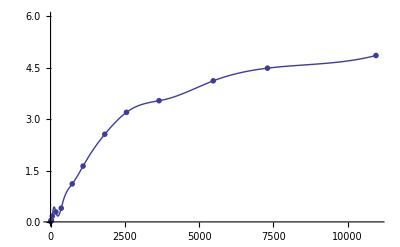

```mathematica
rates = {{7,0.01},{14,0.04},{30,0.05},{60,0.17},{180,0.29},{360,0.4},{730,1.11},{1095,1.63},{1825,2.56},{2555,3.20},{3650,3.54},{5475,4.12},{7300,4.49},{10950,4.86}};
iRates=Interpolation[rates,Method->"Spline"];
Show[
ListPlot[rates,PlotStyle->{PointSize[0.01]},PlotRange->{{0,11000},{0,6}}],
Plot[iRates[t],{t,7,11000}]
]
```

```mathematica
nsYieldCurve[m_,β0_,β1_,β2_,τ_]:=
β0+(β1(1-Exp[-m/τ]))/(m/τ)+β2((1-Exp[-m/τ])/(m/τ)-Exp[-m/τ])
```

```mathematica
fit=FindFit[rates, nsYieldCurve[m,b0,b1,b2,t],
{b0,b1,b2,t},m,Method->NMinimize]
```

{b0→5.28846,b1→-5.26294,b2→-3.75868,t→651.468}

```mathematica
Manipulate[Show[ListPlot[rates,
PlotStyle->{PointSize[0.01]},PlotRange->{{0,11000},{0,6}}]
Plot[nsYieldCurve[m,beta0,beta1,beta2,tau],{m,1,11000},PlotRange->{{0,11000},{0,6}}]],
{{beta0,b0},3,6,0.1},{{beta1,b1},2,-6,0.1},{{beta2,b2},-5,-1,0.1},{{tau,t},100,1000,10},SaveDefinitions->True]/.fit
```

Show::gtype: "Times is not a type of graphics. (*ButtonBox[

Show::gtype: Times is not a type of graphics.